```mathematica
Clear["Global`*"];
```

## Input Data

### Time

```mathematica
T=1.5;
Δt=0.00001;Marching=Round[T/Δt];
```

### Elements

```mathematica
ne=4;(*number of elements*)
nn=5;(*number of nodes*)
odf=9;(*open degree of freedoms*)
```

### Geometry

```mathematica
LL[x1_,y1_,x2_,y2_]:=√((x2-x1)^2+(y2-y1)^2);
θ[x1_,y1_,x2_,y2_]:=If[x2-x1==0,π/2,ArcTan[(y2-y1)/(x2-x1)]];
node={{0,0},{0,1},{5/34^0.5,1+3/34^0.5},{10/34^0.5,1},{10/34^0.5,0}};
elmn={{1,2},{2,3},{3,4},{4,5}};
x1=y1=x2=y2={};
```

```mathematica
Do[
x1=Append[x1,node_⟦elmn_⟦i,1⟧,1⟧];
y1=Append[y1,node_⟦elmn_⟦i,1⟧,2⟧];
x2=Append[x2,node_⟦elmn_⟦i,2⟧,1⟧];
y2=Append[y2,node_⟦elmn_⟦i,2⟧,2⟧],{i,1,ne}];
```

```mathematica
Le=Table[LL[x1_⟦i⟧,y1_⟦i⟧,x2_⟦i⟧,y2_⟦i⟧],{i,1,ne}];
```

```mathematica
θe=N[{Pi/2,0.5404195002705842,-0.5404195002705842,-Pi/2}];
```

### Material And Section Properties

```mathematica
Eee=2.1 10^11;(*(Kg.f)/m^2*)
ρρ=7850;(*kg/m^3*)
A1=9.1×10^-3;(*m^2 IPB220*)
Ii1=8.09×10^-5;(*m^4 IPB220*)
A2=9.1×10^-3;(*m^2 IPE240*)
Ii2=8.09×10^-5;(*m^4 IPE240*)
L1=4;(*m*)
L2=5 34^0.5/5;(*m*)
cd=Cd=0.1;(*cdb*)
cda=0.05;
Ii={Ii1,Ii2,Ii2,Ii1};A={A1,A2,A2,A1};LLL={L1,L2,L2,L1};L=1;
```

## Time Weight Function

```mathematica
Ca1={√(Eee/(ρρ L1^2)),√(Eee/(ρρ L2^2)),√(Eee/(ρρ L2^2)),√(Eee/(ρρ L1^2))};Cb1={√((Eee Ii1)/(ρρ A1 L1^4)),√((Eee Ii2)/(ρρ A2 L2^4)),√((Eee Ii2)/(ρρ A2 L2^4)),√((Eee Ii1)/(ρρ A1 L1^4))};


T1=Ca1* T;
T2=Cb1* T;
Δt1=Ca1* Δt;
Δt2=Cb1 *Δt;

m11a=Table[1/8 Δt1[[i]]^4,{i,ne}];m22a=Table[1/3 Δt1[[i]]^3,{i,ne}];m33a=Table[1/2 Δt1[[i]]^2,{i,ne}];

m11b=Table[1/8 Δt2[[i]]^4,{i,ne}];m22b=Table[1/3 Δt2[[i]]^3,{i,ne}];m33b=Table[1/2 Δt2[[i]]^2,{i,ne}];
```

## Source Function

```mathematica
Period=2.1;ϵ=0.1;
g1[x_]:=If[Δt-0.5≤x,0,If[-0.6≤x,-(x+(0.5-Δt))/Δt,If[-0.7≤x,-(-0.7+(0.5-Δt))/Δt+(x+(0.5-Δt))/Δt,0]]];g2[x_]:=If[x≤0.5-Δt,0,If[x≤0.6,(x-(0.5-Δt))/Δt,If[x≤0.7,(0.7-(0.5-Δt))/Δt-(x-(0.5-Δt))/Δt,0]]];
g2[x_]:=g1[-x];
```

```mathematica
gg1[x_]:=If[0≤Abs[x]≤ϵ,-5Abs[x]+5ϵ,0];
```

```mathematica
Needs["FourierSeries`"]
SSa=13;SSb=27;
η1=L/2+0.145;
η2=L/2+0.145;
AAλ1a=AAλ2a=Table[{},{i,1,ne}];αααa=βββ1a=βββ2a=Table[{},{i,1,ne}];ba1a=ba2a=Table[{},{i,1,ne}];
Do[
Do[
AAλ1a_⟦k⟧=Append[AAλ1a_⟦k⟧,NFourierCoefficient[g1[x],x,i,FourierParameters->{1,(-2π)/Period}]];
AAλ2a_⟦k⟧=Append[AAλ2a_⟦k⟧,NFourierCoefficient[g2[x],x,i,FourierParameters->{1,(-2π)/Period}]];
αααa_⟦k⟧=Append[αααa_⟦k⟧,(-2π i ⅈ)/Period];
βββ1a_⟦k⟧=Append[βββ1a_⟦k⟧,1/Le_⟦k⟧×(-2π i ⅈ)/Period];
βββ2a_⟦k⟧=Append[βββ2a_⟦k⟧,1/Le_⟦k⟧×(2π i ⅈ)/Period];,{i,-SSa,SSa,1}];,{k,1,ne}];
```

```mathematica
AAλ1b=Table[{},{i,1,ne}];αααb=αα=zarib=Table[{},{i,1,ne}];
Do[
Do[
AAλ1b_⟦k⟧=Append[AAλ1b_⟦k⟧,Limit[Sin[π Abs[fg]/SSb]/(π Abs[fg]/SSb), fg -> i ]NFourierSinCoefficient[gg1[x-Period/2],x,i,FourierParameters->{1,-π/Period}]];
αα_⟦k⟧=Append[αα_⟦k⟧,(π i)/Period];,{i,1,SSb,1}];,{k,1,ne}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0500003849284287843971878106616186371313759195800230372697114945}. NIntegrate obtained -1.37101×10^-17 and 2.08598×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0500003849284287843971878106616186371313759195800230372697114945}. NIntegrate obtained 2.68708×10^-17 and 3.87737×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.95000038492842869558617504378633319972458082247612765058875083923}. NIntegrate obtained -1.80217×10^-17 and 5.14552×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Do[
Do[
αααb_⟦k⟧=Append[αααb_⟦k⟧,-αα_⟦k,i⟧ⅈ];
zarib_⟦k⟧=Append[zarib_⟦k⟧,-AAλ1b_⟦k,i⟧/(2ⅈ)];,{i,1,Length[αα_⟦k⟧]}];,{k,1,ne}];
Do[
Do[
αααb_⟦k⟧=Append[αααb_⟦k⟧,αα_⟦k,i⟧ⅈ];
zarib_⟦k⟧=Append[zarib_⟦k⟧,AAλ1b_⟦k,i⟧/(2ⅈ)];,{i,1,Length[αα_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
p1a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t^2/2+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1-(1/2(-cda+√(cda^2+4 α^2))) t)/((1/2(-cda+√(cda^2+4 α^2)))^2)];
p2a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t^2/2+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1-(1/2(-cda+√(cda^2+4 α^2))) t)/((1/2(-cda+√(cda^2+4 α^2)))^2)];
m1a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1)/(1/2(-cda+√(cda^2+4 α^2)))];
m2a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1)/(1/2(-cda+√(cda^2+4 α^2)))];,{k,1,ne}];
```

```mathematica
Do[
p1b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t^2/2+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)- (1/2(-Cd+√(Cd^2-4 α^4))) t-1)/((1/2(-Cd+√(Cd^2-4 α^4)))^2)];
p2b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t^2/2+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)- (1/2(-Cd+√(Cd^2-4 α^4))) t-1)/((1/2(-Cd+√(Cd^2-4 α^4)))^2)];

m1b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)-1)/(1/2(-Cd+√(Cd^2-4 α^4)))];
m2b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)-1)/(1/2(-Cd+√(Cd^2-4 α^4)))];,{k,1,ne}];
```

```mathematica
Do[
Do[
If[
αααa_⟦k,i⟧≠0,
AAλ1a_⟦k,i⟧=AAλ1a_⟦k,i⟧/p1a[k,αααa_⟦k,i⟧,Δt1[[k]]];
AAλ2a_⟦k,i⟧=AAλ2a_⟦k,i⟧/p2a[k,αααa_⟦k,i⟧,Δt1[[k]]];,
ba1a_⟦k⟧=AAλ1a_⟦k,i⟧;ba2a_⟦k⟧=AAλ2a_⟦k,i⟧;];
,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
zarib1=zarib2=zarib3=zarib4=zarib;ba1b=ba2b=ba3b=ba4b=Table[{},{i,1,ne}];

Do[
Do[
zarib1_⟦k,i⟧=zarib_⟦k,i⟧/p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] ⅇ^(αααb_⟦k,i⟧ (-Period/2+η1));
zarib2_⟦k,i⟧=zarib_⟦k,i⟧/(-αααb_⟦k,i⟧p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb_⟦k,i⟧ (-Period/2+η2));
zarib3_⟦k,i⟧=zarib_⟦k,i⟧/p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] ⅇ^(αααb_⟦k,i⟧ (-Period/2-η1));
zarib4_⟦k,i⟧=zarib_⟦k,i⟧/(αααb_⟦k,i⟧p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb_⟦k,i⟧ (-Period/2-η2));,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
h0a=l0a=Table[{},{i,1,ne}];
Do[
h0a_⟦k⟧=ba1a_⟦k⟧/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);l0a_⟦k⟧=ba2a_⟦k⟧/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);

I1a[k_,x_]:=∑_(i=1)^Length[αααa_⟦k⟧] (ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])+h0a_⟦k⟧ (-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);
I2a[k_,x_]:=∑_(i=1)^Length[αααa_⟦k⟧] (ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]])+l0a_⟦k⟧ (-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);,{k,1,ne}];
```

```mathematica
Do[
dis2[k_]=-∑_(i=1)^Length[αααb_⟦k⟧] (p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧);
dis4[k_]=-∑_(i=1)^Length[αααb_⟦k⟧] (p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧);

I1b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧);
I1bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I1bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I1bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);I2b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧)+dis2[k];
I2bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I2bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I2bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);
I3b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧);
I3bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I3bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I3bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);
I4b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧)+dis4[k];
I4bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I4bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I4bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);,{k,1,ne}];
```

## Shape Functions

```mathematica
z1=z2=z3=z4=Table[0{k,ne},{j,4}];
Do[
z1[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{1}, {0}, {0}, {0}});z2[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{0}, {1}, {0}, {0}});z3[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{0}, {0}, {1}, {0}});z4[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{0}, {0}, {0}, {1}});
,{k,1,ne}];
```

```mathematica
ZZ1=ZZ2=ZZ3=ZZ4=Table[0,{k,ne},{j,Length[αααb[[1]]]}];
```

```mathematica
Do[
Do[
ZZ1[[k,i]]=z1[[k,1]]*zarib1_⟦k,i⟧+z1[[k,2]] zarib2_⟦k,i⟧+z1[[k,3]] zarib3_⟦k,i⟧+z1[[k,4]] zarib4_⟦k,i⟧;
ZZ2[[k,i]]=z2[[k,1]]*zarib1_⟦k,i⟧+z2[[k,2]] zarib2_⟦k,i⟧+z2[[k,3]] zarib3_⟦k,i⟧+z2[[k,4]] zarib4_⟦k,i⟧;
ZZ3[[k,i]]=z3[[k,1]]*zarib1_⟦k,i⟧+z3[[k,2]] zarib2_⟦k,i⟧+z3[[k,3]] zarib3_⟦k,i⟧+z3[[k,4]] zarib4_⟦k,i⟧;
ZZ4[[k,i]]=z4[[k,1]]*zarib1_⟦k,i⟧+z4[[k,2]] zarib2_⟦k,i⟧+z4[[k,3]] zarib3_⟦k,i⟧+z4[[k,4]] zarib4_⟦k,i⟧;
,{i,1,Length[αααb[[1]]]}];
,{k,1,ne}];
```

```mathematica
con1=con2=con3=con4=Table[0,{k,ne}];
```

```mathematica
Do[
con1[[k]]=z1[[k,1,1]]*0+z1[[k,2,1]]dis2[k]+z1[[k,3,1]]*0+z1[[k,4,1]]dis4[k];
con2[[k]]=z2[[k,1,1]]*0+z2[[k,2,1]]dis2[k]+z2[[k,3,1]]*0+z2[[k,4,1]]dis4[k];
con3[[k]]=z3[[k,1,1]]*0+z3[[k,2,1]]dis2[k]+z3[[k,3,1]]*0+z3[[k,4,1]]dis4[k];
con4[[k]]=z4[[k,1,1]]*0+z4[[k,2,1]]dis2[k]+z4[[k,3,1]]*0+z4[[k,4,1]]dis4[k];
,{k,1,ne}];
N1b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con1[[k]];
N1bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N1bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N1bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;

N2b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con2[[k]];
N2bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N2bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N2bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;


N3b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con3[[k]];
N3bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N3bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N3bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;

N4b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con4[[k]];
N4bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N4bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N4bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;
```

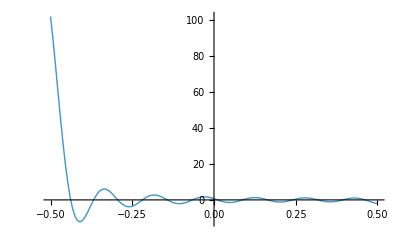

```mathematica
Plot[{Re[N2bααα[2,x]]},{x,-0.5,0.5},PlotPoints->3,PlotRange->All,PlotStyle->Thick]
```

```mathematica
S1a=S2a=Table[{},{i,1,ne}];
Do[
S1a_⟦k⟧=I1a[k,-L/2];S2a_⟦k⟧=I1a[k,L/2];
N1a[k_,x_]:=S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)I1a[k,x]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I2a[k,x];
N2a[k_,x_]:=-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I1a[k,x]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I2a[k,x];,{k,1,ne}];
```

```mathematica
Do[
N1αa[k_,x_]:=(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]));
N2αa[k_,x_]:=(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]));,{k,1,ne}];
```

## Stiffness Matrix

```mathematica
k1[Le_,θ_,el_]:=Transpose[({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})].({{-(Eee×A[[el]])/LLL[[el]]N1αa[el,-L/2], 0, 0}, {0, Eee×Ii[[el]]×N1bααα[el,-L/2], Eee×Ii[[el]]×N2bααα[el,-L/2]}, {0, -Eee×Ii[[el]]×N1bαα[el,-L/2], -Eee×Ii[[el]]×N2bαα[el,-L/2]}}).({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
k2[Le_,θ_,el_]:=Transpose[({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})].({{(Eee×A[[el]])/LLL[[el]]×N2αa[el,L/2], 0, 0}, {0, -Eee×Ii[[el]]×N3bααα[el,L/2], -Eee×Ii[[el]]×N4bααα[el,L/2]}, {0, Eee×Ii[[el]]×N3bαα[el,L/2], Eee×Ii[[el]]×N4bαα[el,L/2]}}).({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
```

```mathematica
ke1=ke2={};
Do[AppendTo[ke1,k1[Le_⟦i⟧,θe_⟦i⟧,i]];
AppendTo[ke2,k2[Le_⟦i⟧,θe_⟦i⟧,i]];
,{i,1,ne}];
```

```mathematica
Table[MatrixForm[ke1_⟦i⟧],{i,ne}];Table[MatrixForm[ke2_⟦i⟧],{i,ne}];
MatrixForm[ke1];
```

```mathematica
t[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
B1=({{1, 2}, {2, 3}, {3, 4}, {4, 5}});
te={};
Do[AppendTo[te,t[θe_⟦i⟧]],{i,1,ne}];
Table[MatrixForm[te_⟦i⟧],{i,ne}];
MatrixForm[te[[1]]];
```

```mathematica
K=Table[0,{i,nn},{j,3},{r,3}];
For[i=1,i≤ne,i++,
For[j=1,j≤2,j++,
If[j==1,K_⟦B1_⟦i,j⟧⟧+=ke1_⟦i⟧,K_⟦B1_⟦i,j⟧⟧+=ke2_⟦i⟧];
];
];
```

### Open degree of freedom

```mathematica
odf1=ReplacePart[Table[3,{i,nn}],{1->0,5->0}];
dof=Table[0,{i,nn},{j,3}];
dof=ReplacePart[dof,{{1,1}->1,{1,2}->1,{1,3}->1,{5,1}->1,{5,2}->1,{5,3}->1}];
```

### Assembling

```mathematica
K1=Kuu={};

Do[
K1=Append[K1,Table[0,{j,odf1[[i]]},{r,3}]];
Kuu=Append[Kuu,Table[0,{j,odf1[[i]]},{r,odf1[[i]]}]];
,{i,1,nn}]
```

```mathematica
For[i=1,i≤nn,i++,
For[j=1,j≤odf1[[i]],j++,
K1_⟦i,j,All⟧=K_⟦i,Ordering[dof[[i]]]_⟦j⟧,All⟧
];
];
For[i=1,i≤nn,i++,
For[j=1,j≤odf1[[i]],j++,
Kuu_⟦i,All,j⟧=K1_⟦i,All,Ordering[dof[[i]]]_⟦j⟧⟧
];
];
```

```mathematica
FF={};
Do[
FF=Append[FF,If[Length[Kuu[[i]]]==0,0,Inverse[Kuu[[i]]]]];
,{i,1,nn}];
```

## Force And Initial Displacement

```mathematica
RR1=Table[0,{i,ne},{k,3},{h,1}];RR2=Table[0,{i,ne},{k,3},{h,1}];R1=Table[0,{j,6 nn},{k,1}];Ru=Table[0,{j,odf},{k,1}];ww=Table[0,{j,nn},{k,3}];wwt=Table[0,{j,6 nn},{k,1}];wwe=Table[0,{i,ne},{k,6},{h,1}];wwe1=Table[0,{i,ne},{k,3},{h,1}];wwe2=Table[0,{i,ne},{k,3},{h,1}];Δwe6=Table[0,{i,ne},{k,6},{h,1}];Δwe61=Table[0,{i,ne},{k,3},{h,1}];Δwe62=Table[0,{i,ne},{k,3},{h,1}];CC=Table[0,{i,ne},{k,4},{h,1}];uB=Table[0,{i,Marching}];


AAa=Table[{},{i,1,ne}];
Do[Do[AAa_⟦k⟧=Append[AAa_⟦k⟧,0],{j,1,Length[αααa_⟦k⟧]}],{k,1,ne}];
AAb=Table[{},{i,1,ne}];
Do[Do[AAb_⟦k⟧=Append[AAb_⟦k⟧,0],{j,1,Length[αααb_⟦k⟧]}],{k,1,ne}];
BBa=Table[{},{i,1,ne}];
Do[Do[BBa_⟦k⟧=Append[BBa_⟦k⟧,0],{j,1,Length[αααa_⟦k⟧]}],{k,1,ne}];
BBb=Table[{},{i,1,ne}];
Do[Do[BBb_⟦k⟧=Append[BBb_⟦k⟧,0],{j,1,Length[αααb_⟦k⟧]}],{k,1,ne}];



disa=Table[{},{i,1,ne}];
Do[disa_⟦k⟧=0,{k,1,ne}];

dis22a=Table[{},{i,1,ne}];
Do[dis22a_⟦k⟧=0,{k,1,ne}];

disb=Table[{},{i,1,ne}];
Do[disb_⟦k⟧=0,{k,1,ne}];

dis22b=Table[{},{i,1,ne}];
Do[dis22b_⟦k⟧=0,{k,1,ne}];(*exponential base coefficients*)
```

```mathematica
BPc={-L/2,L/2};
BPa=Table[0,{k,1,ne},{q,1,2},{i,1,Length[αααa_⟦1⟧]}];
BPb=Table[0,{k,1,ne},{q,1,2},{i,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Do[
BPa_⟦k,q,i⟧=ⅇ^(αααa_⟦k,i⟧×BPc_⟦q⟧);,{i,1,Length[αααa_⟦k⟧]}];,{q,1,2}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Do[
BPb_⟦k,q,i⟧=ⅇ^(αααb_⟦k,i⟧×BPc_⟦q⟧);,{i,1,Length[αααb_⟦k⟧]}];,{q,1,2}];,{k,1,ne}];
```

```mathematica
Ezafea=Table[{},{k,1,ne},{i,1,Length[αααa_⟦1⟧]}];
Ezafeb=Table[{},{k,1,ne},{i,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Ezafea_⟦k,i⟧=Append[Ezafea_⟦k,i⟧,m33a[[k]]/(αααa_⟦k,i⟧^2 m11a[[k]]-cda m22a[[k]]-m33a[[k]])Δt1[[k]]^2/2];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Ezafeb_⟦k,i⟧=Append[Ezafeb_⟦k,i⟧,(αααb_⟦k,i⟧^4  m33b[[k]])/(αααb_⟦k,i⟧^4*m11b[[k]]+cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Source1a=Source2a=Table[{},{i,1,ne},{j,1,Length[αααa_⟦1⟧]}];
Source1b=Source2b=Source3b=Source4b=Table[{},{i,1,ne},{j,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Source1a_⟦k,i⟧=Append[Source1a_⟦k,i⟧,S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];
Source2a_⟦k,i⟧=Append[Source2a_⟦k,i⟧,-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Source1b_⟦k,i⟧=Append[Source1b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ1[[k,i,1]]];
Source2b_⟦k,i⟧=Append[Source2b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ2[[k,i,1]]];
Source3b_⟦k,i⟧=Append[Source3b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ3[[k,i,1]]];
Source4b_⟦k,i⟧=Append[Source4b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ4[[k,i,1]]];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Sourcett1a=Sourcett2a=Table[{},{i,1,ne},{j,1,Length[αααa_⟦1⟧]}];
Sourcett1b=Sourcett2b=Sourcett3b=Sourcett4b=Table[{},{i,1,ne},{j,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Sourcett1a_⟦k,i⟧=Append[Sourcett1a_⟦k,i⟧,S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×m1a[k,αααa_⟦k,i⟧,Δt1[[k]]]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×m2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];
Sourcett2a_⟦k,i⟧=Append[Sourcett2a_⟦k,i⟧,-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×m1a[k,αααa_⟦k,i⟧,Δt1[[k]]]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×m2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Sourcett1b_⟦k,i⟧=Append[Sourcett1b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ1_⟦k,i,1⟧];
Sourcett2b_⟦k,i⟧=Append[Sourcett2b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ2_⟦k,i,1⟧];
Sourcett3b_⟦k,i⟧=Append[Sourcett3b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ3_⟦k,i,1⟧];
Sourcett4b_⟦k,i⟧=Append[Sourcett4b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ4_⟦k,i,1⟧];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
rr=0;
 aa=ab=Table[0,{i,ne}];
```

```mathematica
Do[
aa[[k]]=(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]+Δt1[[k]]^2/2)/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);
ab[[k]]=(-(Cd m11b[[k]]+m22b[[k]])/(Cd m22b[[k]]+m33b[[k]])Δt2[[k]]^1/1+Δt2[[k]]^2/2)/(-(Cd m11b[[k]]+m22b[[k]])/(Cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2+Δt2[[k]]^3/6);,{k,1,ne}];
```

```mathematica
www={};
Do[
www=Append[www,Table[0,{r,odf1[[i]]}]];
,{i,1,nn}];
```

## Load

```mathematica
P=Table[0,{i,Marching},{k,1,nn},{k,3}];
P[[1,4,1]]=1;
```

## Main Program

```mathematica
Do[
COa=AAa(1-Ezafea αααa^2)+BBa(Δt1-Ezafea×((αααa^2 m22a)/m33a-cda));
COαa=αααa×COa;
COb=AAb(1-Ezafeb)+BBb(Δt2-Ezafeb×((m22b)/m33b+cd/αααb^4));
COαb=αααb×COb;
COααb=(αααb)^2×COb;
COαααb=(αααb)^3×COb;


f=fα=Table[{},{i,1,6}];
f1=fα1=Table[{},{i,1,3}];f2=fα2=Table[{},{i,1,3}];


Do[
f1_⟦1⟧=Append[f1_⟦1⟧,Flatten[COa_⟦k⟧].Transpose[BPa_⟦k,1,All⟧,{1}]+dis22a_⟦k⟧(Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2)+disa_⟦k⟧];
f1_⟦2⟧=Append[f1_⟦2⟧,Flatten[COb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]+dis22b_⟦k⟧ Δt2[[k]]+disb_⟦k⟧-(cd m33b[[k]] dis22b_⟦k⟧)/(cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];
f1_⟦3⟧=Append[f1_⟦3⟧,1/LLL[[k]]*Flatten[COαb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];


f2_⟦1⟧=Append[f2_⟦1⟧,Flatten[COa_⟦k⟧].Transpose[BPa_⟦k,2,All⟧,{1}]+dis22a_⟦k⟧ (Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2)+disa_⟦k⟧];
f2_⟦2⟧=Append[f2_⟦2⟧,Flatten[COb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]+dis22b_⟦k⟧ Δt2[[k]]+disb_⟦k⟧-(cd m33b[[k]] dis22b_⟦k⟧)/(cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];
f2_⟦3⟧=Append[f2_⟦3⟧,1/LLL[[k]]*Flatten[COαb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];

,{k,1,ne}];

Do[
fα1_⟦1⟧=Append[fα1_⟦1⟧,-(Eee×A[[k]])/LLL[[k]]×Flatten[COαa_⟦k⟧].Transpose[BPa_⟦k,1,All⟧,{1}]];
fα1_⟦2⟧=Append[fα1_⟦2⟧,(Eee×Ii[[k]])/LLL[[k]]^3×Flatten[COαααb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];
fα1_⟦3⟧=Append[fα1_⟦3⟧,-(Eee×Ii[[k]])/LLL[[k]]^2×Flatten[COααb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];

fα2_⟦1⟧=Append[fα2_⟦1⟧,(Eee×A[[k]])/LLL[[k]]×Flatten[COαa_⟦k⟧].Transpose[BPa_⟦k,2,All⟧,{1}]];
fα2_⟦2⟧=Append[fα2_⟦2⟧,-(Eee×Ii[[k]])/LLL[[k]]^3×Flatten[COαααb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];
fα2_⟦3⟧=Append[fα2_⟦3⟧,(Eee×Ii[[k]])/LLL[[k]]^2×Flatten[COααb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];
,{k,1,ne}];(*Subscript[f, i]^n*)

Do[
RR1_⟦k⟧=(ke1_⟦k⟧.(Transpose[te_⟦k⟧].f1_⟦All,k⟧))-(Transpose[te_⟦k⟧].fα1_⟦All,k⟧);
RR2_⟦k⟧=(ke2_⟦k⟧.(Transpose[te_⟦k⟧].f2_⟦All,k⟧))-(Transpose[te_⟦k⟧].fα2_⟦All,k⟧);
,{k,1,ne}];
RR=Table[0,{i,nn},{k,3},{h,1}];
For[i=1,i≤ne,i++,
For[r=1,r≤2,r++,
If[r==1,RR_⟦B1_⟦i,r⟧⟧+=RR1_⟦i⟧,RR_⟦B1_⟦i,r⟧⟧+=RR2_⟦i⟧];
];
];

Ru={};
Do[
Ru=Append[Ru,Table[0,{r,odf1[[i]]}]];
,{i,1,nn}];

For[i=1,i≤nn,i++,
For[r=1,r≤odf1[[i]],r++,
Ru_⟦i,r⟧=RR_⟦i,Ordering[dof[[i]]]_⟦r⟧⟧
];
];

Do[
If[Length[FF[[i]]]≠0,www[[i]]=FF[[i]].(Ru[[i]]+P[[j,i]])];
,{i,1,nn}];(*u^- and w^-*)

For[i=1,i≤nn,i++,
For[r=1,r≤3,r++,
If[dof_⟦i,r⟧≠1,ww_⟦i,r⟧=Flatten[www_⟦i,r⟧][[1]];
];
];
];

For[ele=1,ele≤ne,ele++,
For[r=1,r≤3,r++,
wwe1_⟦ele,r⟧=ww_⟦B1_⟦ele,1⟧,r⟧;
wwe2_⟦ele,r⟧=ww_⟦B1_⟦ele,2⟧,r⟧;
];
];


Do[
Δwe61_⟦i⟧=te_⟦i⟧.(Flatten[(wwe1_⟦i⟧)-(Transpose[te_⟦i⟧].f1_⟦All,i⟧)]);
Δwe62_⟦i⟧=te_⟦i⟧.(Flatten[(wwe2_⟦i⟧)-(Transpose[te_⟦i⟧].f2_⟦All,i⟧)]);
,{i,1,ne}];

uB[[j]]=Re[ww[[2,1]]];

If[j≠Marching,
BBa=BBa×(1-Ezafea ((αααa^2 m22a)/m33a -cda)2/Δt1)-AAa×Ezafea αααa^2×2/Δt1+Sourcett1a×Δwe61_⟦;;,1⟧+Sourcett2a×Δwe62_⟦;;,1⟧;


BBb=BBb×(1-Ezafeb(m22b/m33b+cd/αααb^4)2/Δt2)-AAb×Ezafeb×2/Δt2+
Sourcett1b×Δwe61_⟦;;,2⟧+Sourcett2b×Δwe61_⟦;;,3⟧+Sourcett3b×Δwe62_⟦;;,2⟧+Sourcett4b×Δwe62_⟦;;,3⟧;


AAa=COa+Source1a×Δwe61_⟦;;,1⟧+Source2a×Δwe62_⟦;;,1⟧;

AAb=COb+Source1b×Δwe61_⟦;;,2⟧+Source2b×Δwe61_⟦;;,3⟧+Source3b×Δwe62_⟦;;,2⟧+Source4b×Δwe62_⟦;;,3⟧;

Do[
disa_⟦k⟧=disa_⟦k⟧+dis22a_⟦k⟧ (Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]]) Δt1[[k]]^2/2)+(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)Δwe61_⟦k,1⟧+(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)Δwe62_⟦k,1⟧;

dis22a_⟦k⟧=dis22a_⟦k⟧ (1-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]])+(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧) (aa[[k]])Δwe61_⟦k,1⟧+(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)(aa[[k]])Δwe62_⟦k,1⟧;

disb_⟦k⟧=disb_⟦k⟧+dis22b_⟦k⟧ (Δt2[[k]]-(cd m33b[[k]])/(cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2)+con1[[k]]×Δwe61_⟦k,2⟧+con2[[k]]×Δwe61_⟦k,3⟧+con3[[k]]×Δwe62_⟦k,2⟧+con4[[k]]×Δwe62_⟦k,3⟧;


dis22b_⟦k⟧=dis22b_⟦k⟧(1-(cd m33b[[k]])/(cd m22b[[k]]+m33b[[k]])Δt2[[k]])+(con1[[k]]×Δwe61_⟦k,2⟧+con2[[k]]×Δwe61_⟦k,3⟧+con3[[k]]×Δwe62_⟦k,2⟧+con4[[k]]×Δwe62_⟦k,3⟧)ab[[k]];
,{k,1,ne}];

];(*Update exponential base coefficients*)
,{j,1,Marching}];
```

## Result

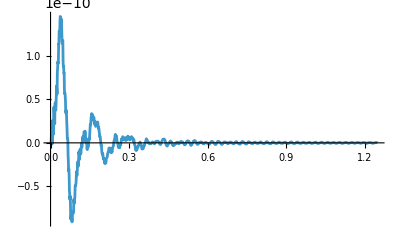

```mathematica
ListPlot[Table[{i Δt,uB[[i]]},{i,1,125000,100}],PlotRange->All,Joined->True]
```

## Load Identification

```mathematica
wwa=Table[0,{i,1,Marching/100}];
Do[
wwa[[i]]=uB[[100i]];,{i,1,Marching/100}];
```

```mathematica
HH=Table[0,{i,Marching/100},{j,Marching/100}];
```

```mathematica
Do[
Do[
HH[[i+j-1,j]]=Re[uB_⟦100(i-1)+1⟧];,{i,1,Marching/100-j+1}];,{j,1,Marching/100}];
```

```mathematica
uz=Transpose[Import["D:\\Desktop\\1.xlsx"]];(*Please,insert the storage path for the horizontal displacement response of node B.*)
```

```mathematica
ee=0.00;
```

```mathematica
DD={};
Do[
DD=Append[DD,(1+ee RandomReal[{-1,1}]) uz[[100i,1]][[1]]];,{i,1,Marching/100}];
```

```mathematica
pp=PseudoInverse[Transpose[HH].HH ].Transpose[HH].DD;
```

```mathematica
nemo1=Table[{100j Δt,pp[[j]]/100},{j,1,Marching/100,5}];
```

```mathematica
nemo2=Table[{100j Δt,If[100j Δt<1.2,1000Sin[500Pi j Δt],0]},{j,1,Marching/100}];
```

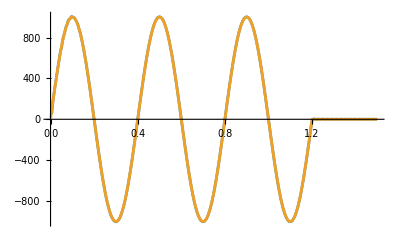

```mathematica
ListPlot[{nemo1,nemo2},Joined->True,PlotRange->All]
```

```mathematica
NN=Marching/100;
DD=Table[0,{i,NN}];
ee=0.01;
Do[
DD[[i]]= uz[[100i,1]][[1]] (1+ee RandomReal[{-1,1}]);
,{i,1,NN}];
```

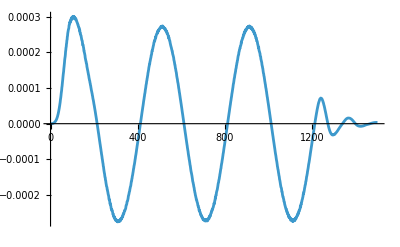

```mathematica
ListPlot[DD,Joined->True]
```

```mathematica
Ee=Table[0,{i,NN},{j,NN}];
Do[
Do[
Ee[[i,j]]=ⅇ^((2 Pi ⅈ)/NN j (i-1));,{i,1,NN}];,{j,1,NN}];
```

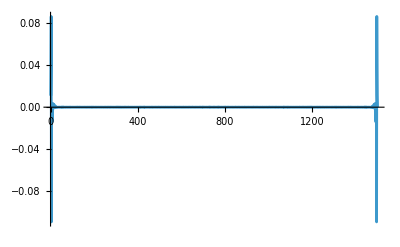

```mathematica
Yk=DD.Ee;
ListPlot[Re[Yk],Joined->True,PlotRange->All]
```

```mathematica
Ykj=Table[0,{i,NN}];
Do[
If[Abs[Re[Yk[[i]]]]≥0.002,Ykj[[i]]=Yk[[i]]/NN;];,{i,1,NN}];
```

```mathematica
Xj=Ykj.Transpose[Ee];
```

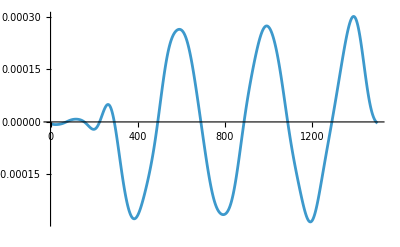

```mathematica
ListPlot[Re[Xj],Joined->True,PlotRange->All]
```

```mathematica
XXj=Table[Xj[[NN-i+1]],{i,1,NN}];
```

```mathematica
pp=PseudoInverse[Transpose[HH].HH ].Transpose[HH].DD;
pp1=PseudoInverse[Transpose[HH].HH ].Transpose[HH].XXj;
```

```mathematica
nemo1=Table[{100j Δt,Re[pp[[j]]/100]},{j,1,Marching/100,5}];nemo11=Table[{100j Δt,Re[pp1[[j]]/100]},{j,1,Marching/100,5}];
```

## Result

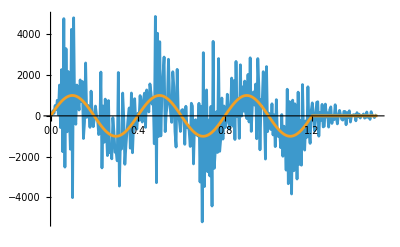

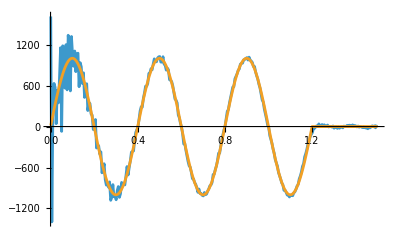

```mathematica
P1=ListPlot[{nemo1,nemo2},Joined->True,PlotRange->All]
P2=ListPlot[{nemo11,nemo2},Joined->True,PlotRange->All]
```